# Atom-cavity QED

P. Huft

```mathematica
SetOptions[Plot,Axes->False,Frame->{True,True,False,False},LabelStyle->Directive[Black, 16],ImageSize->Medium];
SetOptions[ListPlot,Axes->False,Frame->{True,True,False,False},LabelStyle->Directive[Black, 16],ImageSize->Medium];
SetDirectory[FileNameJoin[{NotebookDirectory[],"images\\"}]];
```

## Jaynes-Cumming Model

Dressed states

## Rotating frame

In what follows, the plots can be physically a bit misleading if you are not paying attention: the eigenenergy pairs for each n in reality are offset from each other, as their center of mass depends on n. In the rotating frame, the diagonal terms are pruned of ω0(n-1/2), which is clearly this n-dependent baseline energy.

Consider a single atom interacting with a single mode of the electromagnetic field, i.e. an atom in a cavity. Ignoring dissipation, the system is described by the Jaynes-Cummings Hamiltonian in a rotating frame, where the rotating wave approximation has been made and ℏ=1:
 H=Δc a^†a + Δc σ_+σ_-+g(aσ_++a^†σ_-)
 
 The diagonal terms correspond to the detuning of the field from the cavity resonance and the detuning of the cavity from the atom resonance. 
 
 If the system is driven, an additional term is added for the driving field:
 ϵ(a^†+a)
 
 Ignoring driving for now, we can deal with an effective two level system, in which the basis states are direct products between atomic and photonic states:
 {n,g,n-1,e}. 
 Diagonalizing the Hamiltonian with this uncoupled basis gives us the so-called dressed states and associated energies of the coupled system. 
 
 NOTE: i worked out the algebra for the system in my Leuchtermm notebook page 157.

```mathematica
Clear[Δa,Δc,g,n]
Hjc=({{Δc n, g √n}, {g √n, Δc (n-1)+Δa}});
{evals,evecs}=Eigensystem[Hjc]
```

{{1/2 (Δa-Δc+2 n Δc-√(4 g^2 n+Δa^2-2 Δa Δc+Δc^2)),1/2 (Δa-Δc+2 n Δc+√(4 g^2 n+Δa^2-2 Δa Δc+Δc^2))},{{-(Δa-Δc+√(4 g^2 n+Δa^2-2 Δa Δc+Δc^2))/(2 g √n),1},{-(Δa-Δc-√(4 g^2 n+Δa^2-2 Δa Δc+Δc^2))/(2 g √n),1}}}

```mathematica
evecs
```

{{-(Δa-Δc+√(4 g^2 n+Δa^2-2 Δa Δc+Δc^2))/(2 g √n),1},{-(Δa-Δc-√(4 g^2 n+Δa^2-2 Δa Δc+Δc^2))/(2 g √n),1}}

Plot the eigenvalues for a few different n and reasonable parameters for the detunings wrt to g.

```mathematica
(*strong coupling ~ interaction strength > detunings*)
g=1; 
Δa =0; 
nlist = {1,2,3};
colors = Array[RGBColor[RandomReal[],RandomReal[],RandomReal[]]&,Length[nlist]];
plts = {};
For[i=1, i<Length[nlist]+1,i++,
AppendTo[plts,Plot[evals/.n-> nlist[[i]],{Δc,-5g,5g},PlotStyle->colors[[i]]]];
];
```

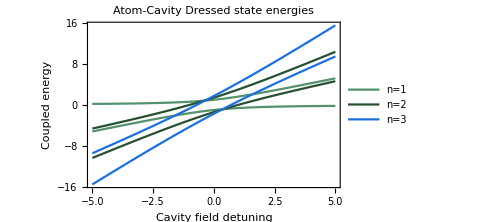

```mathematica
Legended[Show[plts, FrameLabel-> {"Cavity field detuning","Coupled energy"},PlotLabel-> "Atom-Cavity Dressed state energies",PlotRange-> All],LineLegend[colors,Array[StringForm["n=``",nlist[[#]]]&,Length[nlist]]]]
```

```mathematica
Array[StringForm["n=``",nlist[[#]]]&,Length[nlist]]
```

{n=1,n=2,n=3}

Plot for very different n:

```mathematica
(*strong coupling ~ interaction strength > detunings*)
g=1; 
Δa =0; 
nlist = {1,10};
colors = Array[RGBColor[RandomReal[],RandomReal[],RandomReal[]]&,Length[nlist]];
plts = {};
For[i=1, i<Length[nlist]+1,i++,
AppendTo[plts,Plot[evals/.n-> nlist[[i]],{Δc,-5g,5g},PlotStyle->colors[[i]]]];
];
```

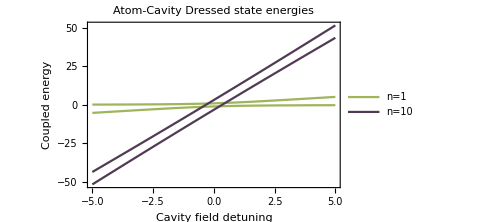

```mathematica
Legended[Show[plts, FrameLabel-> {"Cavity field detuning","Coupled energy"},PlotLabel-> "Atom-Cavity Dressed state energies",PlotRange-> All],LineLegend[colors,Array[StringForm["n=``",nlist[[#]]]&,Length[nlist]]]]
```

Subtracting off the cavity energy with n photons will make the eigenvalues easier to read without losing any information:

```mathematica
Clear[Δa,Δc,g,n]
Hjc=({{0, g √n}, {g √n, -Δc+Δa}});
{evals,evecs}=Eigensystem[Hjc]
```

{{1/2 (Δa-Δc-√(4 g^2 n+Δa^2-2 Δa Δc+Δc^2)),1/2 (Δa-Δc+√(4 g^2 n+Δa^2-2 Δa Δc+Δc^2))},{{-(Δa-Δc+√(4 g^2 n+Δa^2-2 Δa Δc+Δc^2))/(2 g √n),1},{-(Δa-Δc-√(4 g^2 n+Δa^2-2 Δa Δc+Δc^2))/(2 g √n),1}}}

```mathematica
(*strong coupling ~ interaction strength > detunings*)
g=1; 
Δa =0; 
nlist = {1,2,3,10};
colors = Array[RGBColor[RandomReal[],RandomReal[],RandomReal[]]&,Length[nlist]];
plts = {};
For[i=1, i<Length[nlist]+1,i++,
AppendTo[plts,Plot[evals/.n-> nlist[[i]],{Δc,-5g,5g},PlotStyle->colors[[i]]]];
];
```

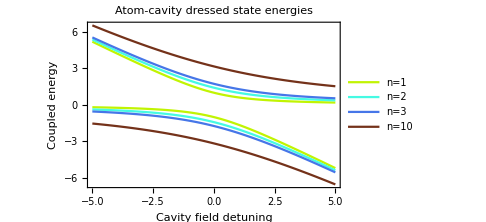

```mathematica
plt=Legended[Show[plts, FrameLabel-> {"Cavity field detuning","Coupled energy"},PlotLabel-> "Atom-cavity dressed state energies",PlotRange-> All],LineLegend[colors,Array[StringForm["n=``",nlist[[#]]]&,Length[nlist]]]]
```

```mathematica
Export[ToString[StringForm["plot_dressed_jc_rotframe_g``_da``_nmax``.png",g,Δa,ωc,nlist[[-1]]]],plt,ImageResolution-> 300]
```

plot_dressed_jc_rotframe_g1_da0_nmax10.png

Eigenvalues without subtracting off the cavity energy:

```mathematica
1/2 (Δa-Δc+2 n Δc±√(4 g^2 n+Δa^2-2 Δa Δc+Δc^2))
```

Eigenvalues after subtracting off the cavity energy:

```mathematica
1/2 (Δa-Δc±√(4 g^2 n+Δa^2-2 Δa Δc+Δc^2))
```

So this choice simply offsets each pair of eigenvalues to be centered around zero. This of course strips away information about the absolute energy in the system, which is n dependent, but allows us to see how the curvature of the fields changes

## Non-rotating frame

Consider a single atom interacting with a single mode of the electromagnetic field, i.e. an atom in a cavity. Ignoring dissipation, the system is described by the Jaynes-Cummings Hamiltonian , where the rotating wave approximation has been made and ℏ=1:
 H=ω a^†a + ω ' σ_+σ_-+g(aσ_++a^†σ_-)
 
 ω0 is the bare atom resonance and ω is the field in the cavity. In the Hamiltonian below, the substitution ω=Δc+ωc, and ω’=Δa+ωa  has been made. 
 
 If the system is driven, an additional term is added for the driving field:
 ϵ(a^†+a)
 
 Ignoring driving for now, we can deal with an effective two level system, in which the basis states are direct products between atomic and photonic states:
 {n,g,n-1,e}. 
 Diagonalizing the Hamiltonian with this uncoupled basis gives us the so-called dressed states and associated energies of the coupled system. 
 
 NOTE: i worked out the algebra for the system in my Leuchtermm notebook page 157.

```mathematica
Clear[Δa,Δc,g,n]
Hjc=({{Δc n+ωc(n-1/2), g √n}, {g √n, Δc (n-1)+Δa+ωc(n-1/2)}});
{evals,evecs}=Eigensystem[Hjc]
```

{{1/2 (-10+20 n+Δa-Δc+2 n Δc-√(4 g^2 n+Δa^2-2 Δa Δc+Δc^2)),1/2 (-10+20 n+Δa-Δc+2 n Δc+√(4 g^2 n+Δa^2-2 Δa Δc+Δc^2))},{{-(Δa-Δc+√(4 g^2 n+Δa^2-2 Δa Δc+Δc^2))/(2 g √n),1},{-(Δa-Δc-√(4 g^2 n+Δa^2-2 Δa Δc+Δc^2))/(2 g √n),1}}}

```mathematica
evecs
```

{{-(Δa-Δc+√(4 g^2 n+Δa^2-2 Δa Δc+Δc^2))/(2 g √n),1},{-(Δa-Δc-√(4 g^2 n+Δa^2-2 Δa Δc+Δc^2))/(2 g √n),1}}

Plot the eigenvalues for a few different n and reasonable parameters for the detunings wrt to g.

```mathematica
(*strong coupling ~ interaction strength > detunings*)
g=1; 
Δa =0; 
nlist = {1,2,3,4};
ωc = 10; (*much much smaller than reality, to make plotting easier*)
colors = Array[RGBColor[RandomReal[],RandomReal[],RandomReal[]]&,Length[nlist]];
plts = {};
For[i=1, i<Length[nlist]+1,i++,
AppendTo[plts,Plot[evals/.n-> nlist[[i]],{Δc,-5g,5g},PlotStyle->colors[[i]]]];
];
```

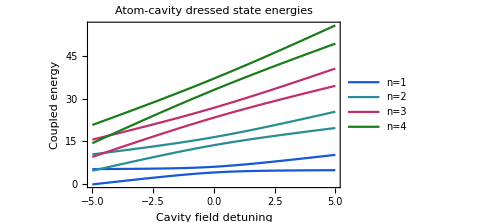

```mathematica
plt=Legended[Show[plts, FrameLabel-> {"Cavity field detuning","Coupled energy"},PlotLabel-> "Atom-cavity dressed state energies",PlotRange-> All],LineLegend[colors,Array[StringForm["n=``",nlist[[#]]]&,Length[nlist]]]]
```

```mathematica
Export[ToString[StringForm["plot_dressed_jc_g``_da``_wc``_nmax``.png",g,Δa,ωc,nlist[[-1]]]],plt,ImageResolution-> 300]
```

plot_dressed_jc_g1_da0_wc10_nmax4.png

Detection

## Atom-cavity lineshape